```mathematica
(* This file is available at https://github.com/grtarnop/PiTP_school_2023https://github.com/grtarnop/PiTP_school_2023Nonehttps://github.com/grtarnop/PiTP_school_2023HyperlinkActionRecycledHyperlinkActive *)
```

### Exact Diagonalization for the XY model with Open Boundary Conditions (OBC)

```mathematica
(* Picture of the chain sites *)
Chain[s_]:=Graphics[Table[{Disk[{i,0},0.1],Text[i,{i,-0.5}]},{i,1,s}]]
```

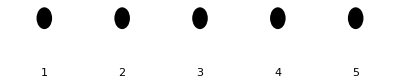

```mathematica
n=5;(* number of the chain sites *)
Chain[n]
```

#### Exact Diagonalization of the isotropic XY spin-1/2 chain with Open Boundary Conditions (OBC)

```mathematica
(* Define σ^+, σ^- and I *)
sp={{0,1},{0,0}}; (* σ^+*)
sm={{0,0},{1,0}}; (* σ^-*)
id={{1,0},{0,1}};(* I *)
Print["σ^+=",sp//MatrixForm,"  ","σ^-=",sm//MatrixForm,"  ","I=",id//MatrixForm]
```

σ^+=(0 | 1
0 | 0)  σ^-=(0 | 0
1 | 0)  I=(1 | 0
0 | 1)

```mathematica
(* Define Hamiltonian term h[i] = Subscript[σ, i]^+Subscript[σ, i+1]^- + Subscript[σ, i]^-Subscript[σ, i+1]^+ *)
(* Define tensor product of m 2 x 2 identity matrices: Id[m] = Subscript[I, 1] ⊗ Subscript[I, 2] ⊗ Subscript[I, 3] ⊗ ... ⊗ Subscript[I, m] *)
Id[m_]:=IdentityMatrix[{2^m,2^m}];
Id[2]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(* Define Hamiltonian term h[i] = Subscript[I, 1] ⊗ ... ⊗ Subscript[I, i-1] ⊗ (Subscript[σ, i]^+ ⊗ Subscript[σ, i+1]^- + Subscript[σ, i]^- ⊗ Subscript[σ, i+1]^+) ⊗ Subscript[I, i+2] ⊗ ... ⊗ Subscript[I, n] *)
h[i_]:=SparseArray[KroneckerProduct[KroneckerProduct[Id[i-1],KroneckerProduct[sp,sm]+KroneckerProduct[sm,sp]],Id[n-i-1]]]
```

```mathematica
(* Construct XY Hamiltonian Subscript[H, XY] = ∑_(i=1)^(n-1) (Subscript[σ, i]^+Subscript[σ, i+1]^- + Subscript[σ, i]^-Subscript[σ, i+1]^+) *)
HXY=∑_(i=1)^(n-1) h[i];
```

```mathematica
HXYsparse=SparseArray[HXY//N];
```

```mathematica
(* Find highest magnitude spectrum of the Subscript[H, XY] Hamiltonian *)
Sort[Eigenvalues[HXYsparse,10]]
```

{-2.73205,-2.73205,-1.73205,-1.73205,-1.73205,1.73205,1.73205,1.73205,2.73205,2.73205}

#### Exact theoretical results for the XY model spectrum (Lieb Schultz Mattis)

```mathematica
(*The ground state energy of the isotropic XY model with OBC*)
ϵ[k_,n_]:=-2 Cos[(π k)/(n+1)];
E0exact[n_]:=∑_(k=1)^Floor[n/2] ϵ[k,n]
```

```mathematica
E1exact[n_]:=∑_(k=1)^(Floor[n/2]-1) ϵ[k,n]
E1bexact[n_]:=∑_(k=1)^(Floor[n/2]+1) ϵ[k,n]
```

```mathematica
(* Exact values of the energy *)
E0exact[n]//N
E1exact[n]//N
E1bexact[n]//N
```

-2.73205

-1.73205

-2.73205